## Generating Figures for the Appendix of the article “Obscuring digital route choice information prevents delay-induced congestion”

## Appendix A: Linear stability analysis

Figure 7: Maximal real eigenvalues for a given in-rate

In Figure 7, we plot the maximal real parts of the solutions of the characteristic equation that corresponds to the differential equations of our two-street model. 
Essential part of the differential equations are the travel times on streets 1 and 2:

```mathematica
(*Travel times*)
t1[ N0_,N1_]:=(Exp[N1/N0]-1)/(N1/N0);
t2[N0_,N2_]:=(Exp[N2/N0]-1)/(N2/N0);
```

With these, the differential equations that give the change of the number of vehicles on either street with time are:

```mathematica
(*Differential equations*)
DGLN1τ[ν_, N1_, N2_, N1τ_, N2τ_, N0_]:=(ν/(1+Exp[t1[N0, N1τ]-t2[N0, N2τ]]))-(N1^2)/(N0*(Exp[N1/N0]-1));
DGLN2τ[ν_, N1_, N2_,N1τ_, N2τ_, N0_]:=(ν/(1+Exp[t2[N0, N2τ]-t1[N0, N1τ]]))-(N2^2)/(N0*(Exp[N2/N0]-1));
```

From the differential equations, we find the entries of the two Jacobi matrices:

```mathematica
(*Jacobi matrices*)
J011r=D[DGLN1τ[ν, N1, N2, N1τ, N2τ, N0], N1];
J012r=D[DGLN1τ[ν, N1, N2, N1τ, N2τ, N0], N2];
J021r=D[DGLN2τ[ν, N1, N2, N1τ, N2τ, N0], N1];
J022r=D[DGLN2τ[ν, N1, N2, N1τ, N2τ, N0], N2];
```

```mathematica
Jτ11r=D[DGLN1τ[ν, N1, N2, N1τ, N2τ, N0], N1τ];
Jτ12r=D[DGLN1τ[ν, N1, N2, N1τ, N2τ, N0], N2τ];
Jτ21r=D[DGLN2τ[ν, N1, N2, N1τ, N2τ, N0], N1τ];
Jτ22r=D[DGLN2τ[ν, N1, N2, N1τ, N2τ, N0], N2τ];
```

For each in-rate below a maximal value, a stable fixed point exists, which we find as follows:

```mathematica
(*Stable fixed point*)
findFixedPoint[N00_,ν0_]:=Min[Table[FindRoot[DGLN1τ[ν0, Nx, Nx, Nx, Nx, N00]==0, {Nx,x0}][[1,2]],{x0,0.1,1.5}]]
```

Now, the characteristic equation is:

```mathematica
(*Characteristic equation*)
form1[λ_, τ_,N00_,ν0_,fp_]:=(J011r+Exp[-λ*τ]Jτ11r-λ)*(J022r+Exp[-λ*τ]*Jτ22r-λ)-(J021r+Exp[-λ*τ]*Jτ21r)*(J012r+Exp[-λ*τ]*Jτ12r)/.N0->N00/.ν->ν0/.N1->fp/.N2->fp/.N1τ->fp/.N2τ->fp;
```

For a given effective capacity N00, an in-rate ν0 and a delay τ, we find now all eigenvalues at the fixed point and determine then the one with maximal real part.

```mathematica
(*Initial conditions {Re,Im} for the root search*)
testRegion={Range[-1,1,0.2],Range[-1,1,0.2]};

findMaxReEigenvalue[N00_,ν0_,τ_,testRegion_List]:=Block[
{fp=findFixedPoint[N00,ν0]},
Max[Re/@Flatten[Table[FindRoot[form1[λ,τ,N00, ν0,fp],{λ,x+RandomReal[{-0.01,0.01}]+y*I+RandomReal[{-0.01,0.01}]*I}][[1,2]],{x,testRegion[[1]]},{y,testRegion[[2]]}]]]
]
```

```mathematica
MaxRealTau4=Table[{ν, findMaxReEigenvalue[1,ν, 4, testRegion]}, {ν, 0.8, 1.4, 0.05}];
MaxRealTau8 = Table[{ν, findMaxReEigenvalue[1,ν, 8, testRegion]}, {ν, 0.8, 1.4, 0.05}];
```

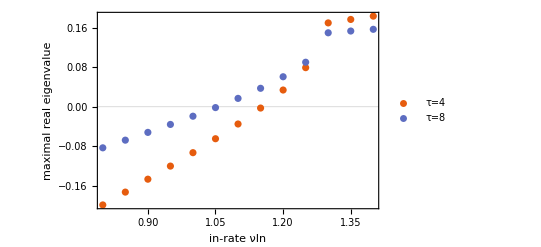

```mathematica
ListPlot[{MaxRealTau4, MaxRealTau8}, 
PlotTheme->"Scientific",
FrameLabel->{"in-rate νIn", "maximal real eigenvalue"},
PlotLegends->{"τ=4", "τ=8"}]
```

Figure 8: Imaginary and real parts of the critical eigenvalue

To find the oscillation period of the critical eigenvalue, we first determine the stability boundary for fixed delay by interval-halving:

```mathematica
(*Interval halving to find the stability boundary for a given delay τ*)
findStabilityBoundaryFixedDelay[N00_,τ_]:=
Module[{minInRate=0.9*N00,maxInRate=1.4*N00,minReEv,maxReEv,midReEv},

minReEv=findMaxReEigenvalue[N00, minInRate, τ,testRegion];
maxReEv=findMaxReEigenvalue[N00, maxInRate, τ,testRegion];

While[(maxInRate-minInRate)>0.001,
If[minReEv<0∧maxReEv>0,
midReEv=findMaxReEigenvalue[N00, (minInRate+maxInRate)/2, τ,testRegion];
If[midReEv<0,minInRate=(minInRate+maxInRate)/2;minReEv=midReEv;,maxInRate=(minInRate+maxInRate)/2;maxReEv=midReEv;],
Break[];
];
];

If[(maxInRate-minInRate)≤0.001,
Return[{(minInRate+maxInRate)/2,True}];,
Return[{maxInRate,False}];
];
]
```

With this, we can then find the imaginary part of the maximal real eigenvalue, which gives us the frequency of the dominant mode at the bifurcation point.

```mathematica
complexEV[τ_, N00_]:=Module[{ν, fp, EVs, LoI, SortedLoI, ComplexMaxEV},
ν= findStabilityBoundaryFixedDelay[N00, τ][[1]];
fp= findFixedPoint[N00, ν];
EVs= Table[λ/.FindRoot[form1[λ,τ,N00, ν,fp],{λ,x+RandomReal[{-0.01,0.01}]+y*I+RandomReal[{-0.01,0.01}]*I}], {x, Range[-1,1,0.2]},{y, Range[-1, 1, 0.2]}];
LoI=ReIm[Flatten[EVs]];
SortedLoI = SortBy[LoI, First];
ComplexMaxEV = Abs[SortedLoI[[-1, 2]]];
Return[ComplexMaxEV];

]
```

```mathematica
periodValues= Table[{τ, 2*Pi/complexEV[τ, 1]}, {τ, 3, 20}];
```

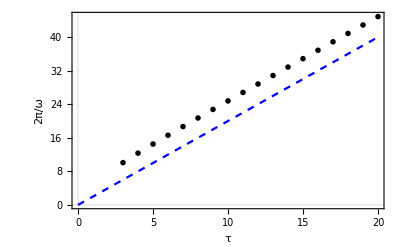

```mathematica
plt1=ListPlot[periodValues, 
PlotRange->{{0, 20}, {0, 45}},
PlotMarkers->{Automatic,Small},
PlotStyle->Black , 
PlotTheme-> "Scientific", 
FrameLabel->{Style["τ", FontSize->14],Style["2π/ω", FontSize->14]},
 LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14], 
FrameTicks->{{All, None}, {All, None}}];
plt2= Plot[2τ, {τ, 0, 20}, PlotStyle->{Blue,Dashed},  
 LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14]];
Show[plt1, plt2]
```

For a given in-rate and delay, the eigenvalues in the complex plane can be found as follows:

```mathematica
N0V=1;
ν0V=1.2;
τ0V=5;

EVs[τ_, ν0_, fp_]:= Table[λ/.FindRoot[form1[λ,τ,N0V, ν0,fp],{λ,x+RandomReal[{-0.001,0.001}]+y*I+RandomReal[{-0.001,0.001}]*I}], {x, Range[-2,2,0.2]},{y, Range[-15, 15, 0.1]}];

bifν5=findStabilityBoundaryFixedDelay[N0V, τ0V];
fp1 = findFixedPoint[N0V, bifν5[[1]]];
LoI1=ReIm[Flatten[EVs[τ0V, bifν5[[1]], fp1]]];
```

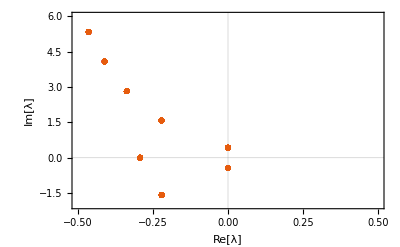

```mathematica
ListPlot[LoI1, 
PlotMarkers->{Automatic, Medium},
PlotRange->{{-0.5, 0.5}, {-2, 6}},
PlotTheme->"Scientific", 
FrameLabel->{Style["Re[λ]", FontSize->14], Style["Im[λ]", FontSize->14]},
 LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14], 
FrameTicks->{{All, None}, {All, None}},
BaseStyle->Opacity[.98]]
```

## Appendix B: Robustness of results for a fraction of informed drivers

Figure 9 a: Homogeneous two-street network

In a homogeneous street network, free flow travel times on both streets are equal.

```mathematica
Quit[]
```

```mathematica
t01=1;
t02=1;
N0=1;
β=1;
```

```mathematica
(*Travel times*)
t1[ t01_, N0_,N1_]:=t01*(Exp[N1/N0]-1)/(N1/N0);
t2[t02_,N0_,N2_]:=t02*(Exp[N2/N0]-1)/(N2/N0);
```

When only a fraction of drivers f is informed, the in-rate consists of a part (1-f) of drivers that choose their routes randomly, and another part f that respond to the information.

```mathematica
(*In-rates*)
rIN1[β_,t01_, t02_,N0_, N1_, N2_, f_]:=f*1/(1+Exp[β*(t1[t01,N0,N1]-t2[t02,N0,N2])])+(1-f)/2;
rIN2[β_,t01_, t02_,N0_, N1_, N2_, f_]:=f*1/(1+Exp[-β*(t1[t01,N0,N1]-t2[t02,N0,N2])])+(1-f)/2;
```

```mathematica
(*Differential equations*)
EqN1τ[ν_, β_, t01_, t02_, N0_, f_, t_, τ_, N1init_]:={D[N1[t], t]==(ν*rIN1[β,t01, t02,N0, N1[t-τ], N2[t-τ], f])-(N1[t]^2)/(t01*N0*(Exp[N1[t]/N0]-1)), N1[t/;t≤0]==N1init};
EqN2τ[ν_, β_, t01_, t02_, N0_, f_, t_, τ_, N2init_]:={D[N2[t], t]==(ν*rIN2[β,t01, t02,N0, N1[t-τ], N2[t-τ], f])-(N2[t]^2)/(t02*N0*(Exp[N2[t]/N0]-1)), N2[t/;t≤0]==N2init};
```

```mathematica
(*Function to determine the solution of the delay differential equations numerically*)
SolsDDE[νIN_, N1init_, N2init_, f_,t_, τ_, tfin_]:={NDSolve[Flatten[{EqN1τ[νIN, β, t01, t02, N0, f, t, τ, N1init], EqN2τ[νIN, β, t01, t02, N0, f, t, τ, N2init], {WhenEvent[(N1[t]+N2[t])==10, {Set[t0,t], "StopIntegration"}], WhenEvent[t==tfin-1, Set[t0,tfin]]}}], {N1[t], N2[t]}, {t, 0,tfin}][[1]], t0};
```

```mathematica
DGLN1τ[ν_, N1_, N2_, N1τ_, N2τ_, N0_,f_]:=(ν*(f*1/(1+Exp[β*(t1[1,N0,N1]-t2[1,N0,N2])])+(1-f)/2))-(N1^2)/(N0*(Exp[N1/N0]-1));
(*Stable fixed point*)
findFixedPoint[N00_,ν0_,f_]:=Min[Table[FindRoot[DGLN1τ[ν0, Nx, Nx, Nx, Nx, N00, f]==0, {Nx,x0}][[1,2]],{x0,0.1,1.5}]]
```

To find the critical in-rate for given τ and a certain fraction of informed drivers f, we solve the differential equation for each in-rate and check whether the street loads grow over time. The critical in-rate is the one at which for a certain tuple f and τ the solution is unstable for the first time.

```mathematica
MaxDiff[νIN_, t_, τ_, tfin_,f_]:=Module[
{fp,LastTime, FirstMax, SecondMax},
fp=findFixedPoint[N0, νIN, f];
LastTime=SolsDDE[νIN,fp+0.1,fp-0.1, f, t, τ, tfin][[2]]-2;
FirstMax=FindMaxValue[{(N1[t]+N2[t])/.Evaluate[SolsDDE[νIN,fp+0.1,fp-0.1, f, t, τ, LastTime]][[1]], t≥LastTime/10 && t≤2*LastTime/10}, t];
SecondMax=FindMaxValue[{(N1[t]+N2[t])/.Evaluate[SolsDDE[νIN,fp+0.1,fp-0.1, f, t, τ, LastTime]][[1]], t≥LastTime*(8/10)&& t<LastTime*(9/10)}, t];
Return[SecondMax-FirstMax]]
```

```mathematica
CheckStability[f_, τ_]:= Module[
{DiffVal, ν, foundν},
ν=0.5;
foundν=False;
While[foundν==False,
DiffVal=MaxDiff[ν, t, τ, 500, f];
If[DiffVal ≥0.1, foundν=True, ν+=0.01];
 ];
Return[ν]
]
```

```mathematica
StabBoundτ0=Table[{f,CheckStability[f, 0]}, {f, 0, 1, 0.05}];
StabBoundτ5=Table[{f,CheckStability[f, 5]}, {f, 0, 1, 0.05}];
StabBoundτ15=Table[{f,CheckStability[f, 15]}, {f, 0, 1, 0.05}];
```

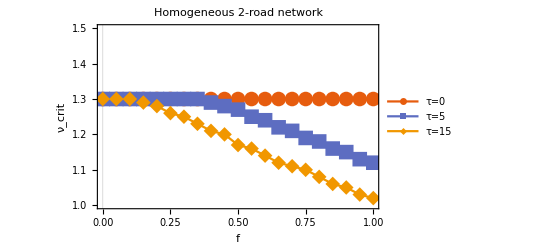

```mathematica
ListLinePlot[{StabBoundτ0, StabBoundτ5, StabBoundτ15}, 
PlotRange->{{0, 1},{1, 1.5}},
PlotLegends->{"τ=0", "τ=5", "τ=15"},
PlotLabel->"Homogeneous 2-road network",
PlotMarkers->{Automatic, 15}, PlotTheme->"Scientific",
FrameLabel->{"f", "ν_crit"},
LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14], 
FrameTicks->{{All, None}, {All, None}}]
```

Figure 9 b: Heterogeneous two-street network

In a heterogeneous street network, free flow travel times on both streets differ.

```mathematica
Quit[]
```

```mathematica
t01=1;
t02=2;
N0=1;
β=1;
```

```mathematica
(*Travel times*)
t1[ t01_, N0_,N1_]:=t01*(Exp[N1/N0]-1)/(N1/N0);
t2[t02_,N0_,N2_]:=t02*(Exp[N2/N0]-1)/(N2/N0);
```

When only a fraction of drivers f is informed, the in-rate consists of a part (1-f) of drivers that choose their routes randomly, and another part f that respond to the information.

```mathematica
(*In-rates*)
rIN1[β_,t01_, t02_,N0_, N1_, N2_, f_]:=f*1/(1+Exp[β*(t1[t01,N0,N1]-t2[t02,N0,N2])])+(1-f)/2;
rIN2[β_,t01_, t02_,N0_, N1_, N2_, f_]:=f*1/(1+Exp[-β*(t1[t01,N0,N1]-t2[t02,N0,N2])])+(1-f)/2;
```

```mathematica
(*Differential equations*)
DGLN1τ[ν_, β_, t01_, t02_, N0_, f_, t_, τ_, N1init_]:={D[N1[t], t]==(ν*rIN1[β,t01, t02,N0, N1[t-τ], N2[t-τ], f])-(N1[t]^2)/(t01*N0*(Exp[N1[t]/N0]-1)), N1[t/;t≤0]==N1init};
DGLN2τ[ν_, β_, t01_, t02_, N0_, f_, t_, τ_, N2init_]:={D[N2[t], t]==(ν*rIN2[β,t01, t02,N0, N1[t-τ], N2[t-τ], f])-(N2[t]^2)/(t02*N0*(Exp[N2[t]/N0]-1)), N2[t/;t≤0]==N2init};
```

```mathematica
(*Function to determine the solution of the delay differential equations numerically*)
SolsDDE[νIN_, N1init_, N2init_, f_,t_, τ_, tfin_]:={NDSolve[Flatten[{DGLN1τ[νIN, β, t01, t02, N0, f, t, τ, N1init], DGLN2τ[νIN, β, t01, t02, N0, f, t, τ, N2init], {WhenEvent[(N1[t]+N2[t])==10, {Set[t0,t], "StopIntegration"}], WhenEvent[t==tfin-1, Set[t0,tfin]]}}], {N1[t], N2[t]}, {t, 0,tfin}][[1]], t0};
```

To find the critical in-rate for given τ and a certain fraction of informed drivers f, we solve the differential equation for each in-rate and check whether the street loads grow over time. The critical in-rate is the one at which for a certain tuple f and τ the solution is unstable for the first time.

```mathematica
MaxDiff[νIN_, t_, τ_, tfin_,f_]:=Module[
{init,LastTime, FirstMax, SecondMax},
init=0.1;
LastTime=SolsDDE[νIN,init,init, f, t, τ, tfin][[2]]-2;
FirstMax=FindMaxValue[{(N1[t]+N2[t])/.Evaluate[SolsDDE[νIN,init, init, f, t, τ, LastTime]][[1]], t≥LastTime/10 && t≤2*LastTime/10}, t];
SecondMax=FindMaxValue[{(N1[t]+N2[t])/.Evaluate[SolsDDE[νIN,init, init, f, t, τ, LastTime]][[1]], t≥LastTime*(8/10)&& t<LastTime*(9/10)}, t];
Return[SecondMax-FirstMax]]
```

```mathematica
CheckStability[f_, τ_]:= Module[
{DiffVal, ν, foundν},
ν=0.5;
foundν=False;
While[foundν==False,
DiffVal=MaxDiff[ν, t, τ, 500, f];
If[DiffVal ≥0.1, foundν=True, ν+=0.01];
 ];
Return[ν]
]
```

```mathematica
StabBoundτ0=Table[{f,CheckStability[f, 0]}, {f, 0, 1, 0.05}];
StabBoundτ5=Table[{f,CheckStability[f, 5]}, {f, 0, 1, 0.05}];
StabBoundτ15=Table[{f,CheckStability[f, 15]}, {f, 0, 1, 0.05}];
```

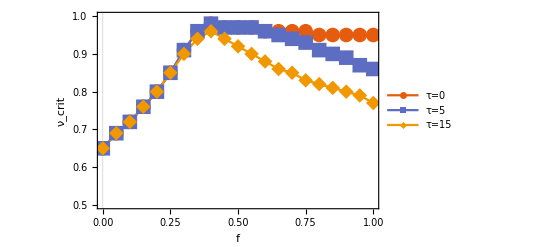

```mathematica
ListLinePlot[{StabBoundτ0, StabBoundτ5, StabBoundτ15}, 
PlotRange->{{0, 1},{0.5, 1}},
PlotLegends->{"τ=0", "τ=5", "τ=15"},
PlotMarkers->{Automatic, 15}, PlotTheme->"Scientific",
FrameLabel->{"f", "ν_crit"},
LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14], 
FrameTicks->{{All, None}, {All, None}}]
```